# Complexity Analysis of Climate Data during Last Deglaciation Maria Yu Qian Lim 500386873

## Abstract

This report consists of seven sections. In the first section, a brief introduction of events in last deglaciation period, importance of studying paleoclimate records and some previous work findings are discussed. The second section describes the dataset used in this project, and followed by third section where preprocessing of data is showed. The main results of this project are found in Section 4 and 5, where complexity of time series is analysed and critical slowing down for abrupt climate changes is indicated respectively. In Section 6, a comparative analysis with linear data is performed. The report is wrapped up by a conclusion and suggestion for future work in the last section.

## 1. Introduction

There were many events happened during the last deglaciation period [1], such as the Dansgaard Oeschger or DO oscillations, Bolling Allerod warming, and Younger Dryas. D-O oscillations are the most dramatic and frequent abrupt climate changes in the geological record, and studies had proven that it is not just a regional phenomena but hemispheric-wide effect.[2] Bolling Allerod interstadial ran from 14,690 to 12,890 years before the present (BP). [3] It began with the end of the cold period known as the Oldest Dryas, and ended abruptly with the onset of the Younger Dryas. On the other hand, Younger Dryas which happened from around 12,900 to 11,700 years BP , was a return to glacials condition which temporarily reversed the climatic warming.[4] This temperature change occurred at the end of the Pleistocene epoch and immediately before the current, warmer Holocene epoch. In this study the latter two events are focused, same as many other previous studies on paleoclimate records.  

The purpose of studying the switching between one climate state and another is to, at least, try to understand the underlying dynamics of the global climate system, although they are still unclear. [5] It is concerned that human activities that speed up the global warming could tip the climate out of its current stable regime since the beginning of Holocene interglacial epoch. Many studies had been carried out on the paleoclimate records to detect early warning signals before a change of system state happened. Most studies focused on two abrupt warming events during the last deglaciation, and the interested period of study is usually from the Last Glacial Maximum (LGM) [6] to the end of the Younger Dryas or to the start of the Bølling-Allerød. For example, Lenton and Livina found that both autocorrelation function (ACF) and detrended fluctuation analysis (DFA) indicators and variance show an increasing trend to the end of the Younger Dryas. [c] Using autocorrelation at lag 1 method, Dakos et al. observed a marked increase in slowing down before the end of Younger Dryas but only weak signs of slowing down for Bolling Allerod warming. [b]

## 2. Dataset

The Greenland Ice Sheet Project 2 (GISP2) ice core temperature data from National Geophysical Data Center is used. [7] The raw climate record consists of 1632 data points, from 50 000 years before present until present. Note that before present is a time scale used mainly in disciplines such as archaeology, where “present” is usually referred to 1 Jan 1950.

```mathematica
data=Reverse[Import["C:\\Users\\maria\\OneDrive\\Documents\\1USyd\\2nd_sem\\CSYS5040\\Assessment\\Assessment 3\\greenland.xlsx",{"Dataset",1},"HeaderLines"->1]]
```

1632

1632

TimeSeries[…]

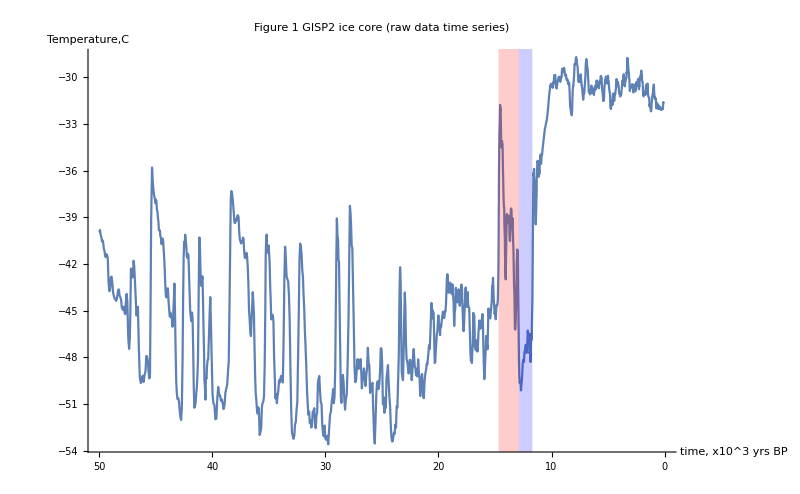

```mathematica
AgeRaw= data[All,"Age"];
TemperatureRaw = data[All,"Temperature (C)"];
Length[AgeRaw]
Length[TemperatureRaw]
tsRaw = TimeSeries[Table[{AgeRaw[[i]],TemperatureRaw[[i]]},{i,Length[TemperatureRaw]}]]
Show[{
ListLinePlot[tsRaw,ScalingFunctions->{"Reverse",Identity}, PlotRange->All,AxesLabel->{RawBoxes["time, x10^3 yrs BP"],RawBoxes["Temperature,C"]},PlotLabel->"Figure 1 GISP2 ice core (raw data time series)",LabelStyle->{GrayLevel[0],Bold},ImageSize->800],
Plot[-60,{x,-12.9,-11.7},PlotStyle->Blue,Filling->Axis],
Plot[-60,{x,-14.69,-12.89},PlotStyle->Red,Filling->Axis]
}]
```

The red band marks the Bølling-Allerød warming and the blue the Younger Dryas. The period for these two climate events are based on the time given on Wikipedia. It is important to check if the climate data is regularly-sampled before processing or carrying out any further analysis. In Mathematica, it is just one step to confirm with this, which is shown below. The result shows that the data in fact is not equidistant.

```mathematica
RegularlySampledQ[tsRaw]
```

False

## 3. Pre-processing and preparation of data

The climate data is resampled and interpolated so that it is transformed to a temporally consistent time series, and ensured by the function “RegularlySampledQ[]”.  The processed data consists of 1996 data points starting from 0.0951 to 50 thousand ages before present, with a time step of 0.025 thousand ages. By this, the record is then presented in its data points itself to be better handled in various analyses which are discussed in following sections. Another significant step in time series processing is to detrend and induce stationary so that the real complexity of data can be captured rather than its seasonal cycles or trends. In this study, the data is detrended by taking the difference of a time data and its previous point. Other common ways adopted by researchers are using log-ratio transformation[a], and Gaussian kernel smoothing function[b,c]. Before applying it to different complexity measures, one can visualise the abrupt changes in climate record just from the plot of differenced data (see Figure 3), where it shows that the differences of data are minimum (points settle around zero) during the last part of the data set which corresponds to the holocene epoch.

```mathematica
tsReg=TimeSeriesResample[tsRaw,0.025,ResamplingMethod->{"Interpolation",InterpolationOrder->0}]
RegularlySampledQ[tsReg]
```

TimeSeries[…]

True

```mathematica
AgeReg = Reverse[tsReg["Times"]];
TemperatureReg =Reverse[tsReg["Values"]];
Length[AgeReg];
Length[TemperatureReg];
TableView[Table[{AgeReg[[i]],TemperatureReg[[i]]},{i,Length[TemperatureReg]}],AllowedDimensions->{2,Length[TemperatureReg]}];
```

1996

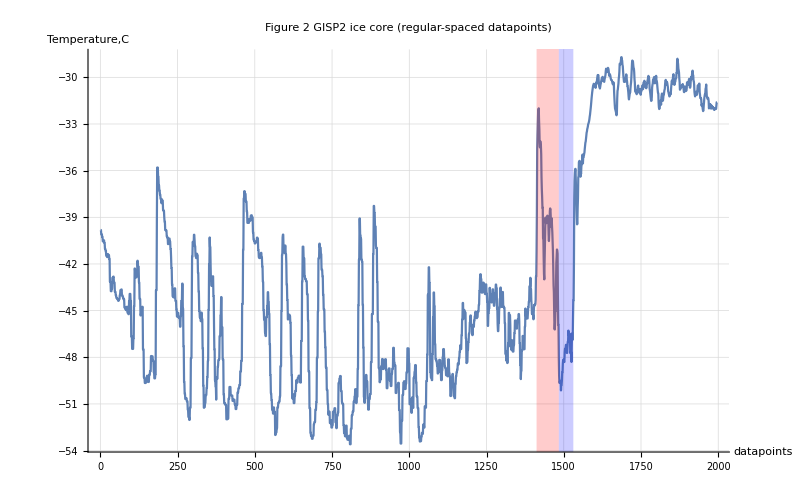

```mathematica
regulardataAll = Table[TemperatureReg[[i]],{i,Length[TemperatureReg]}];
Length[regulardataAll ]
L1 =ListPlot[regulardataAll ,GridLines->Automatic,Joined->True,PlotRange->All,AxesLabel->{RawBoxes["datapoints"],RawBoxes["Temperature,C"]},PlotLabel->"Figure 2 GISP2 ice core (regular-spaced datapoints)",LabelStyle->{GrayLevel[0],Bold},ImageSize->800];
Show[{
L1,
Plot[-60,{x,1412,1484},PlotStyle->Red,Filling->Axis],
Plot[-60,{x,1484,1531},PlotStyle->Blue,Filling->Axis]
}]
```

1995

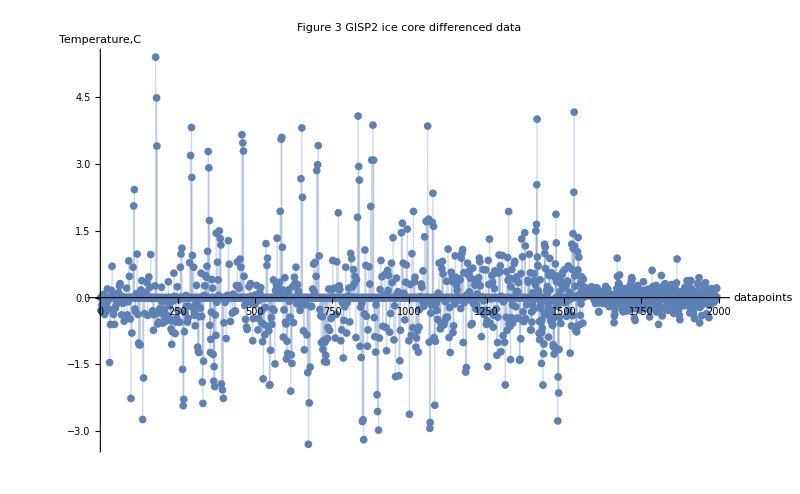

```mathematica
diffdataAll= Differences[regulardataAll];
Length[diffdataAll]
ListLinePlot[diffdataAll,Joined->False,Filling->Axis,PlotRange->All, AxesLabel->{RawBoxes["datapoints"],RawBoxes["Temperature,C"]},PlotLabel->"Figure 3 GISP2 ice core differenced data",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

## 4. Time Series Analysis

In this section, recurrence plots are first plotted for the whole climate record to visualise the nature of the system, and a few measures of complexity based on the plot is carried out. Then, changes of state and complexity of the record are investigated using Hurst exponent, sample entropy and burstiness via a rolling window.

### 4.1 Recurrence plot and RQA

Recurrence of a system to its former states is the fundamental of many dynamical systems. [d] Recurrence plots (RPs) are graphical tools that depict the different occasions when dynamical systems visit the same region of phase space and hence revealing complex deterministic patterns in dynamical systems: [e] 
R_(i,j) (ϵ) = Θ ( ϵ - ‖ (x⃗)_i- (x⃗)_j‖), 	i,j = 1,2,3,...,N
where N is the number of measured points (x⃗)_i, ϵ is a threshold distance, Θ (.) is a Heaviside function (i.e. Θ (x) = 0, if x <0, and Θ (x)=1 otherwise) and ‖.‖ is a norm. [d]
The length of diagonal lines which is parallel to the main diagonal line, Line of Identity reveals the nature of the system. One should expect long diagonal lines for predictable system, and short diagonal lines or even isolated points for stochastic system. [e] Selection of an appropriate ϵ has been a key question in Recurrence Quantification Analysis (RQA), and the fact that it strongly depends on the considered system [d], a value of ϵ = 0.15 standard deviation of climate time series is adopted in this study, based on the suggestion in [f]. The Recurrence Rate (RR) and Determinism (DET) are then calculated by using the Mathematica code adapted from [g]. The former estimates the probability that a certain state recurs while the latter provides an indication of determinism and predictability in the system. [e]

```mathematica
0.15*StandardDeviation[regulardataAll]
```

1.11145

```mathematica
ϵ=1.1;  

g1=MatrixPlot[Table[1-UnitStep[ϵ-Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧]],
{t,1,Length[regulardataAll]},{τ,1,Length[regulardataAll]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Full"];

g2=MatrixPlot[Table[1-UnitStep[ϵ-Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧]],
{t,1,600},{τ,1,600}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Top Left (1-600 datapoints)"];

g3=MatrixPlot[Table[1-UnitStep[ϵ-Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧]],
{t,600,1320},{τ,600,1320}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Centre (600-1320 datapoints)"];

g4=MatrixPlot[Table[1-UnitStep[ϵ-Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧]],{t,1200,Length[regulardataAll]},
{τ,1200,Length[regulardataAll]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Bottom Right (1200-1996 datapoints)"];

Show[ GraphicsGrid[{{g1,g2},{g3,g4}}], PlotLabel-> Style["Figure 4 Recurrence Plot with distance = 1.1","Subsubsection"]]
```

-Graphics-

```mathematica
g5=MatrixPlot[Table[Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧],{t,1,Length[regulardataAll]},{τ,1,Length[regulardataAll]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Original Data"];

g6=MatrixPlot[Table[Norm[diffdataAll⟦t⟧-diffdataAll⟦τ⟧],{t,1,Length[diffdataAll]},{τ,1,Length[diffdataAll]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ},PlotLabel->"Differenced Data"];

Show[GraphicsGrid[{{g5,g6}}], PlotLabel-> Style["Figure 5 Recurrence Plot with all distances","Subsubsection"]]
```

-Graphics-

From Figure 4, it is observed that the temperature is characterised by larger distances in the upper left quadrant (the big square which covers most of the area) of the plot, and small distances in the lower right corner. This suggests that these indices underwent a notable evolution in the period covered by the data. The lower right quadrant in fact covers the Holocene period data points, where the temperature became warmer. According to [e], “butterfly” shaped structure on RP is unique and its position might be related to some sharp changes. From Figure 4 bottom right plot, there is a “butterfly” recurrence structure occurs at the middle upper left, and the position of this shape in fact is the Bølling Allerød warming period.

Looking at the RP with all distances (see Figure 5), two distinct squares of the plots again revealed that the transition of temperature between the squares, and the bands around point 1500 from original data plot could be related to both Bølling Allerød warming and the end of Younger Dryas (starting of Holocene).

```mathematica
ϵ=1.1;
rp =Table[UnitStep[ϵ-Norm[regulardataAll⟦t⟧-regulardataAll⟦τ⟧]],{t,1,Length[regulardataAll]},{τ,1,Length[regulardataAll]}];
n=Length[regulardataAll];
countlines=0;
countpoints=0;
For[j=0,j<n,j++,
linelength=0;
For[i=1,i+j<n,i++,
If[rp[[i,i+j+1]]==1,linelength++,
If[linelength≥2,countlines++,
If[linelength==1,countpoints++
];
];
linelength=0(*reset for a diagonal*)
];
];
If[linelength≥2,countlines++,
If[linelength==1,countpoints++
];
];
];
pr=N[(Total[Total[rp]])/(n*n)];
pd=N[2*countlines/(n*n)];
dr=N[pd/pr];
Print[StringJoin["Recurrence Rate (RR): ",ToString[pr]]];
Print[StringJoin["Determinisim(DET): ",ToString[dr]]];
```

Recurrence Rate (RR): 0.121143

Determinisim(DET): 0.164696

As reported from the code, the RR and DET of the system are 0.12 and 0.16 respectively. These measures are related to the length of diagonal lines in the recurrence matrix [d], hence, low values actually indicate that the low probability of a certain state recurs in this system and so the low determinism and predictability of the system, which is expected to see for climate records.

### 4.2 Hurst Exponent

Hurst Exponent is a measure of long-term memory of time series. If 1>H>0.5,there are long range time correlations, for 0.5>H>0, the series has long range anti-correlations, and if H=1.0, the process is deterministic while uncorrelated noise or random walk corresponds to H=0.5 [h]. The direct relationship of Hurst exponent and fractal dimension (which gives a measure of the roughness of a surface) is known by D = 2- H. The predictability index of temperature is then defined by PI_T= 2|D-1.5|. [h] Interpretation of this index is simple: a value close to 0 indicates the corresponding process approximates the usual Brownian motion (as D = 1.5) and is therefore unpredictable while close to 1, the process is said to be very predictable. In this study, the single value of Hurst Exponent for whole climate record is first calculated. Then, a moving window of size 50 (which is approximately the length of Younger Dryas event) is applied for the record to detect the change of persistency in the data.

```mathematica
windowPlot[data_,window_,f_,plegend_,color_,plabel_,xlabel_,ylabel_]:= Module[{movingmap,xAxis,windowedData,movingaverage,graph1,graph2,plot},
movingmap = MovingMap[f, data,window];
xAxis = Range[window,window+Length[movingmap]];
windowedData =  Table[{xAxis[[i]],movingmap [[i]]},{i,Length[movingmap ]}];
movingaverage = MovingAverage[windowedData,window];
graph1=ListLinePlot[windowedData, GridLines->Automatic,PlotStyle->{color}, PlotRange->{{0,Length[data]},Full},PlotLegends->{plegend}];
graph2 = ListLinePlot[movingaverage, PlotStyle->{Green},PlotLegends->{"Averange value"}];
plot = Show[graph1,graph2,AxesLabel->{RawBoxes[xlabel],RawBoxes[ylabel]},PlotLabel->plabel,LabelStyle->{GrayLevel[0],Bold},ImageSize->800];
plot]
```

```mathematica
hurstExp[data_] :=h/.( FindProcessParameters[data,FractionalBrownianMotionProcess[h]])
```

```mathematica
Hvalue = hurstExp[regulardataAll] 
Dfractal = 2 - Hvalue
Pindex = 2*Abs[Dfractal - 1.5]
```

0.841255

1.15875

0.682509

The Hurst for the whole record is 0.84, which tells the long-term memory  and high persistence of the temperatures in Greenland before present. The Fractal Dimension is 1.16 and the Predictability Index is 0.68, suggests that the temperature data is far from random but also unpredictable. Figure 6 shows the moving window analysis of Hurst exponent over the data. From the figure, it is observed that in overall the time series exhibits reinforcing behaviour through time, with great fluctuations of persistency during the DO event and becomes relatively stable during the LGM. A final jump of H-value is seen onset of Holocene period, and the temperature depicts a very strong correlated behaviour entering the Holocene epoch.

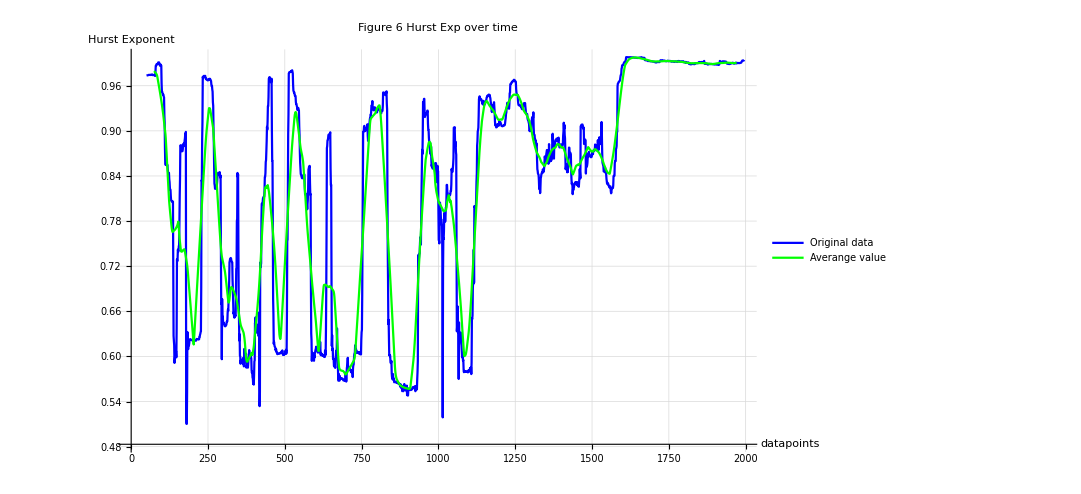

```mathematica
windowPlot[regulardataAll,50,hurstExp,"Original data",Blue,"Figure 6 Hurst Exp over time","datapoints","Hurst Exponent"]
```

### 4.3 Sample Entropy

Sample entropy (SampEn) is one of the regularity statistics been widely used to quantify randomness and complexity and is useful to classify systems and applicable to stochastic and deterministic processes [a]. Larger values of denote higher complexity and lower values imply organization and a higher degree of predictability. The Mathematica code applied is adapted from [i]. Similar to the previous part, a value of SampEn for whole data is first calculated, and followed by the rolling window time series. In order to avoid the cyclic behavior of the temperature influencing the obtained results, and the usefulness of SampEn to determine the complexity could be compromised, it is suggested by [j] to use the stationary version of data rather than the raw data. Two parameters, embedding dimension or the size of the template being compared, m and noise filter r where points within a distance of r are considered equal, are set to 2 and 0.2σ respectively, as suggested in [a,j].

```mathematica
SampEn[data_]:=Module[{m,r,nF1,nF2,diff1,diff2,va1,va2},
m =2;
r =0.2*StandardDeviation[data];
va1=Partition[data,m,1];
va2=Partition[data,1+m,1];
nF1=Nearest[va1->Automatic,DistanceFunction->ChessboardDistance];
nF2=Nearest[va2->Automatic,DistanceFunction->ChessboardDistance];
diff1=Total[(Length/@nF1[va1,{All,r}])]-Length[va1];
diff2=Total[(Length/@nF2[va2,{All,r}])]-Length[va2];
-Log[N@(diff2/diff1)]]
```

```mathematica
SampEn[diffdataAll]
```

1.17748

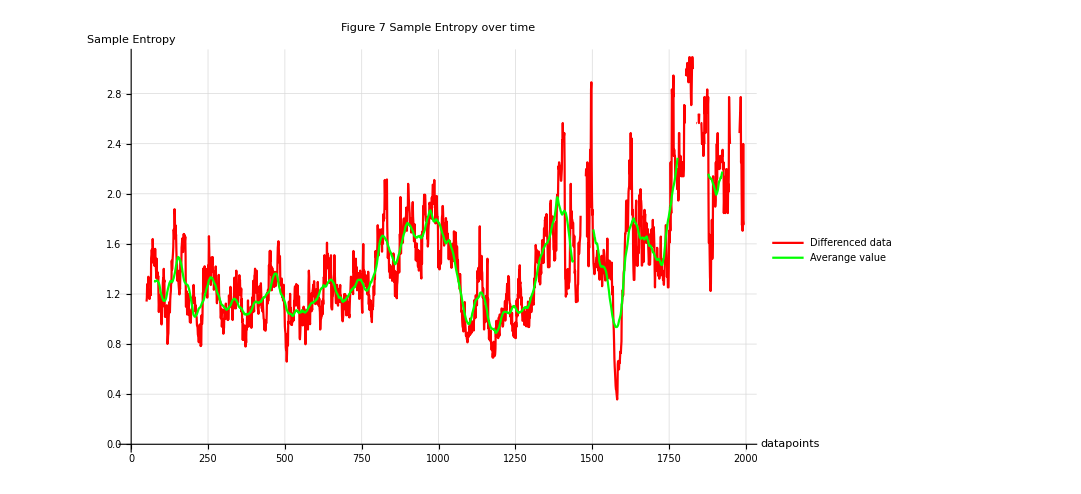

```mathematica
windowPlot[diffdataAll,50,SampEn,"Differenced data",Red,"Figure 7 Sample Entropy over time","datapoints","Sample Entropy"]
```

Using a window of 1250 ages, the trend in Figure 7 shows that the complexity of the temperature in Greenland from 50 thousand ages before present fluctuates around 1.25 and increased slightly when entering LGM before a drop. The complexity then increases by time and eventually reaches a peak of 2.8 at the end of Bølling Allerød warming. This peak is then followed by a plummet to the lowest value at 0.35. Tracing back to the time series, this is actually the time after entering Holocene epoch, where the temperature raises linearly before stabilised at around -30°C.

### 4.4 Burstiness

Burstiness is a measure of the dispersion of a probability distribution where high values represent high volatility relative to the mean and therefore high complexity. [k] One of the measures of burstiness is the Fano Factor like the coefficient of variation, which is a ratio between the variance and the mean or absolute mean. [l,m] In this study, burstiness is measured using a modified coefficient of variation, (c^-)_v from [k]:
(c^-)_v= ( c_v-1)/(c_v+1), where c_v=σ/|μ|

```mathematica
burstiness[data_]:= Module[{std, mean, coeff,burst},
std := StandardDeviation[data];
mean :=Abs[Mean[data]];
coeff:=std/mean;
burst:= (coeff-1)/(coeff+1);
burst]
```

```mathematica
burstiness[diffdataAll]
```

0.987912

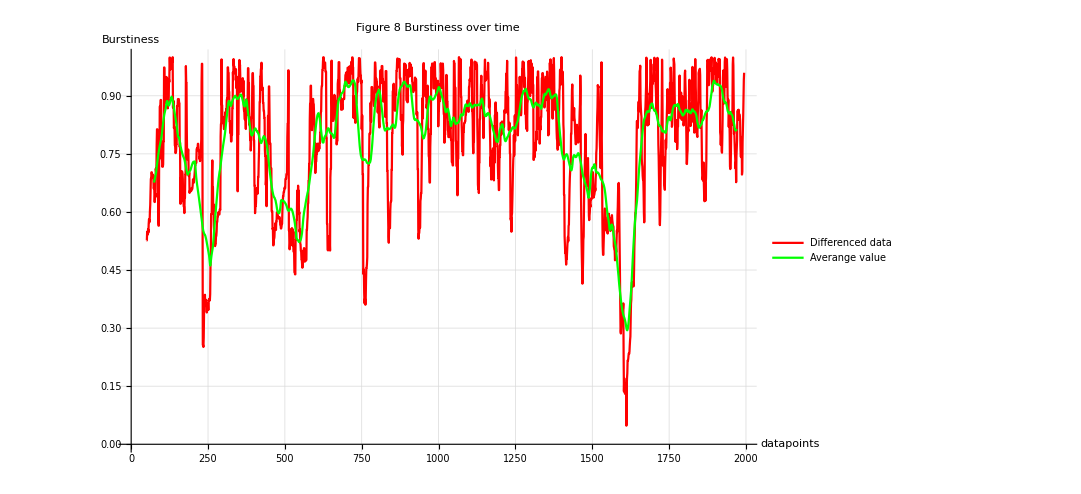

```mathematica
windowPlot[diffdataAll,50,burstiness,"Differenced data",Red,"Figure 8 Burstiness over time","datapoints","Burstiness"]
```

The burstiness of the data is 0.987. Figure 8 reveals the changes in burstiness of stationary data rolling over a window size of 50. The trend of complexity based on burstiness changes and fluctuates sharply before LGM, and becomes relatively stable and high after LGM. It is noticed that the burstiness begins to drop while approaching the Bølling Allerød warming, and continue to decrease until after the end of Younger Dryas. The complexity shoots up after reaching the trough, and relatively stable at value above 0.8 during the Holocene period.

## 5. Critical Slowing Down

In this section, the climate record is cropped so that the dynamics and transitions of temperatures during Bolling Allerod Warming and end of Younger Dryas can be better captured. The aim is to use several indicators to detect early warning signals of those well-known abrupt climate changes during last deglaciation. The idea is based on the generic phenomenon called “critical slowing down”, that in the vicinity of many kinds of tipping points, the recovery rate of a system from small perturbations becomes very slow. [n] It can be inferred indirectly from rising “memory” in small fluctuations in the state of a system, as reflected, for instance, in a higher lag-1 autocorrelation, increased variance, change in skewness and kurtosis. In this study, the moving window size is taken as the half of the number of data points, as suggested in [b].

TimeSeries[…]

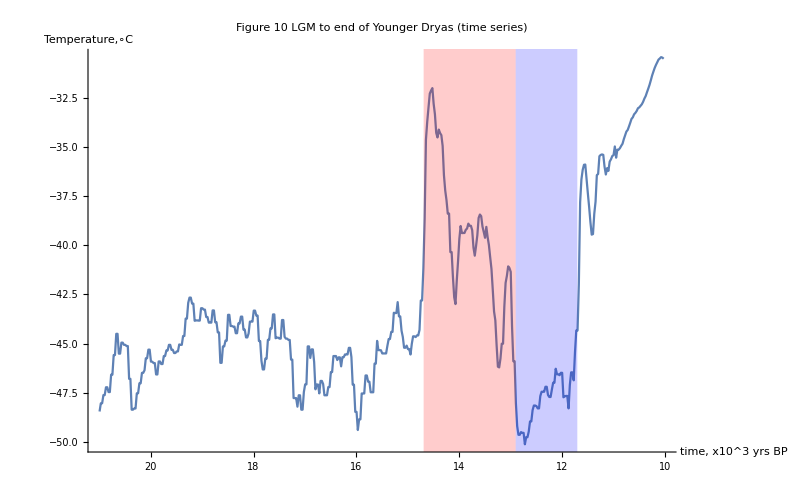

```mathematica
tsPart = TimeSeriesWindow[tsReg,{10,21}]
Show[
ListLinePlot[tsPart,ScalingFunctions->{"Reverse",Identity}, PlotRange->{{10,21},All},AxesLabel->{RawBoxes["time, x10^3 yrs BP"],RawBoxes["Temperature,∘C"]},PlotLabel->"Figure 10 LGM to end of Younger Dryas (time series)",LabelStyle->{GrayLevel[0],Bold},ImageSize->800],
Plot[-60,{x,-12.9,-11.7},PlotStyle->Blue,Filling->Axis],
Plot[-60,{x,-14.69,-12.9},PlotStyle->Red,Filling->Axis]
]
```

```mathematica
AgePart= Reverse[tsPart["Times"]];
TemperaturePart=Reverse[tsPart["Values"]];
Length[AgePart]
Length[TemperaturePart]
regulardataPart = Table[TemperaturePart[[i]],{i,Length[TemperaturePart]}];
TableView[Table[{AgePart[[i]],TemperaturePart[[i]]},{i,Length[TemperaturePart]}],AllowedDimensions->{2,Length[TemperaturePart]}]
```

440

440

1:eJxdmXl4TtcWxlOzqDmVkFLDN4/nG2pskpU5Yp5jdiliDi2NIRQ3SlTQIjFr
Q82ahhIqaaKGomYqURQxNre9QUwldJ+z1rYe7T99fp/nee3z7nevtfbWZPC4
rkPL+fj4ZL/l46P+f8qI8wvyX3rheb8xh162jsnzKz/W2PepF+Kbjk6cUjEm
b/uqyvml95mjmn/VJ7XYC60ioyc8OxWdd+1U61LjLWZN76oX+p7bX+S3Ohr1
Cpg1vTNe+DGpYcvh+6NR7zizpnfIC1P9dkRfjyW9XGZNL9sL+onlVlQ5HoV6
3zFrelu9MLhWXKtdEIV6G5g1vTVeMK6bl3k9Pwr10pk1vcVeSEm9+eC9KaQ3
n1nTS/aCpfUXx2fMJb3pzJpeoheyGyUXd1lEeuOZNb1RXrjTcOPdmGH0vUOZ
Nb0BXqg1pfnWYCftRxyzptfFC8KtiBFG2o92zJpepBc6qh98kPSCmTW9ll44
4G/oVnE27YeLWdOzeuFharePdSG0Pj2zptfIC45F6566HKQX4IWbfg2P3vqd
vrc2s6ZXzQvWz+oVntxI/lVkxvx5oM6GnHz/x+TfU2bMnwdi1IC8Ir1iZsyf
B5p/kNN1WVuZP2bMnwe+3tXi6YFS0jvDjPnzwGNTv4UHKsr8MWP+PLDpcLsW
887Q+rKZMX8eGOEzbmaF7TJ/zJg/z5t5WeN5My/pHkgYWPlk/c0yf8yYPw84
XjUpe5wj88eM+fNAvZEdHqbulPljxvx5YNL4wOrXkmX++O/H/P1rfQM8sGaA
+XitTqQXx4z584Bwt0nqlUjKHzPmzwPvlY7umTQpkvLngZFXx6ekdo+k/DFj
/jzQX5SfrKmkZ2XG/Hng2brhO/8oJr1GHogsKCmNvUd6AcyYPw+kZF6/t/QP
0qvGjPnzQP0bcf57lpPeS/drxvy5ofOLgI8ufk1695kxf27wjxG/nCO9W8yY
PzfcnL3mxJYnpFfAjPljxvy5wRqw9HzVTaR3iBnz5wblB2PNao9IL5sZ8+eG
heJ4prWQ+WPG/Lmhwp3PTX+WyfwxY/7cEHZq2IU7X8j8MWP+3JCrLLcEjJH5
Y8b8uaFSHb+QwwdpfYnMmD833Hm++f7Z6jJ/zJg/NySFvD9gX22ZP2bMnxtG
jCtJPvqBzB8z5k+sZ20D55UXMn/MmD833C+N7T3ntMwfM+bPDU8qDUxvryc9
KzPmzw0XEu8ZXHG0vkbMmD83FA6c1KlRsKx/bmjRIK9v4/syf8yYP2bMnwtW
VAlcM2BzZF5dLX/MmD8XRMwffef5UZk/ZsyfC2KuT/HbMY7Wd5VZ0ytwQfXx
2+b/ViLrnwtK6onAmmT/Zcb8uSD9ypefJd8gvVxmTS/bBT3Xbt1eMFzWP2bM
nwvnhYYyf8yYPxd0bbv6U8MB+t50ZsyfC4J8L2Yk9Jf5E9+rbnhvmT9mzJ8L
juzLXlBpEK0vkRnz54LFNUUDvU3+jWLG/Lng8sWZH0V1l/n7l17cv/S6uMBV
Zdu7feJl/pgxfy44PMb76Z67pBfMrOm1dMHOt8WGFMn+y4z5Y8b8uWBZlvgh
MIby54JN759o0/FMNOoFMGP+XK/nBcwfM+bPBZVFvN/ZT/3tpQL1K/SsYU8h
vafMmD8F/qwuTrysB8XMmD8Fjn8VufvhFZk/BYZfuDPS+o3MHzPmT4GoJY8r
DXwq+68CvmpAtsj8KVBVxN88X/ZfZsyfAnP6iIHyIK3vOwX9+Yj828qM+VNg
lUd0/Lmkt0Z507905U3/FjNj/hSo9/z4X0dXkl4yM+ZPgd3viB9akV4iM+ZP
gVy1P56R9Y8Z88eM+VPg1JNuRRuKZf4UOOtztVzVSzJ/zJg/BUJ69f3uRz9a
X6QCN+4tzXq7UOaPGfOnwCLXJ/YmR0jPxYz5Y8b8KZDx1v6KdVbJ+seM+VOg
h2LZXLdA1j8FRPeKb/o5+VeNGfOnQJPMCfGLg2LySs9uCpxd5nzNhkqXO+4u
ceL+7YzJ69Oq5qx7RU6cN8fG5C0YHfb9uxeZ89ZOvNvpmBPnj0PRqJfDrOll
Mmt6GU4o2rDyYOPO0aiXxqzppTjxvCaSXhKzppfgBOdY4UAO6Q1h1vR6MWt6
sU4IG3TrdNPypBfErOkpTlCvB9ljo1CvmRP+5xQNfmsU6vkza3q+Tpgs2k+V
bVHknwOKjqT/sCwvivxjRv+Y0T9m9M8BbdWBMpX0chwQIK4DGYNJL5MZ/XOA
mI4fmbykl8aM/jmgZ9KO3YP3RJJ/DjjXQVxA9kaSf8zonwP+6hMWfHd8JPnn
gKO3Qtb/fjKS/GNG/xywPkF0CCutT3GA3+mIgpLu0j8HjK4qJsaV0j9m9M8B
annLWiD9s8MfFby1m6+X/jGjf3a49eC9s+OOSP/skHR6Z+9HM6V/dgh0XtFV
6iL9Y0b/7Dhv9ZD+2bGetZP+MaN/dmikDvAG0kuyw8+Vg1b2GC79Y0b/7Hj+
l0SQf3Y4Wb/LpcDO4eSfneb3UPLPDi/E+NXhEpB/dmjfYl7ooCQg/+xgUAfU
pkD+2eFY9/xN62sA+WfHel8WQv7ZoIk68A8lvRIbiNus49Vm0iuygWrX3qah
5J+N7uOh5J8NLgVO+4+7Oq0vxwZZDnGAdKHknw3nc1co+WeDGuoAmkh6aTZI
nib+hvfDyD8biOl06fnlYeSfDSL+/rM4rzCM/KM/d4WTfzbo3tW4bp4STv7Z
KF8R5B8z+meDpqkTxweeiCD/bHAtt8YqT1faj2Y2aJNwcu7Z6ZRnfxv6e4v0
fG1QWx0ohkXkPdT8s8LxWuKHC+Hkn5XyResrskJ0+cRqukxa30UrqMet37e0
v8eYNb0cK6i4cAXpZVrhe3Hd/fAL0suwwrQHmZ1HTSC9NCvU6PTtkqGfkl4K
s6aXZIW7hdv+7rea9BKseB5rRJB/VvAvPPmkW7jMnxXva+Wlf1aIUxtqLukF
WaGiOF4fdCA9xQrlRDvxa0Hra2aFTb2OuQ+G0vr8rXjfSKb1+Vrpfkx6ZRZQ
r5s7Tkr/LHheP5P+WWhelv5ZoDBoctymMumfBdTjOrMD7UeOBTZOPmJuvYL2
N9MC561D699oTPubYYECMS4u2UH7m2aBBWlj68y+S/UqxQLqePBTShT5ZwH1
uvZ9Pdk/LBA668aR9EDZPyygtoPfrlM96GWBQwtFA5b1JZYZ/bNA2eOJ11Yt
pnqgWCBxygZbeCntRzMLlFMfWA7TfvhboLu4Dr6aK/NnAfX55cmXMn9meq+g
7y0xw7btBQMn1ZT1zwz9L0eVT3wo6x8z+md+/T6I/pnJP+rnmWZIe7Vo+vOz
1M8zmNE/M9538qmfp5ih8RDREQ6TXhIz+meG8eoFoVZb8s+M/ekG6fViRv/M
sHj689YJuaQXZAb37R36m1NJT2FG/8xwpulvz6a7Sc/fjP3Nj/R8mdE/E84/
AXJ+MYF2nTHI+YUZ/TPB7C7il19pPjhmgtvq+9++aPKPGf1jRv9MVN/k/MKM
/plgpuHAnI2nSC/JBOL0bxl0WeaPGf0zwZyWvx4as03OLyZ8T5wh5xdm9M+E
77U6Ob+YYMss8UExpNeMGf0z4XtQR9LzNWF9DCa9MuNrRv+MMPHLgAo9r5Je
kRHU566JBaR30QiP08SF9IL0jxn9M772G/0zYr1eIP0z4n63kf4xo39GWF17
Q07+OOmfET78pX+7n/dQP08w4jxmpfMxhBn9M+J98YWsf0ZYe2LLqQu3w8g/
Iwya1KlRva7UjxQj/D195P6P64aRf0bsvw+ov/kbYc/gGYVB96lf+hphZgVR
ETqRXpkBRFpH7t9GeiUGOo+y/hnAR/0vXtY/A/arfbL+GSB26mxn+92yfxgo
/7J/GEBUl3eLb9D6Mgyw/2OxQc3DyD8DDJs7pP9lh+y/Bvz3hH2h5J8Buoxa
8cmqLOrnCQa8j35L/XyIAZb/sGxRzSz63l4Get+l7401wE/nRAF2S/8MYFYb
ZhXpnwF2/Twpd20D6Z8BHsX2ntPyqvTPAEfVPz4l/TPA/LKhT27upfWV6SH/
mBhodtL6SvSgrzRzafhUWl+RHi7HiwJ5UM4vepw/Fsn5hRn908OjvZdSypLl
/KLH/jRJzi96aK8OcCPk/KIHt1pA2pFeih40u93SPz0Y1QeGBtI/PXyoFuBa
0j89bF7fEeo+o3mtl+C6YiC+RvNarB5aNxM7fATIPz2elxw5/+mx38p5rZke
38fWyflPj+8FS+T8pwcxrfVQZpFemQ7f26bJ+U8H00Scvpkg5z8dqP98MyWe
9C7q8L05jvSO6SD0/pBf+oeTXo4OvOoDvZv0MnU4rzQgvQwd7BLj5KVypJem
w/nsXAj5p4OVasFMDyH/dDh/9gkh/3SgtpNgUwj5pwPRnb+Z/CSY/NOBcL95
g9PB5J8O76fbg8k/0ksJJv90kLX6/xsPTw0m/3SgPl8FjSQ9fx2oz2/xCaTn
q4M2b3X4b/UZwXn/AHOpnQQ=

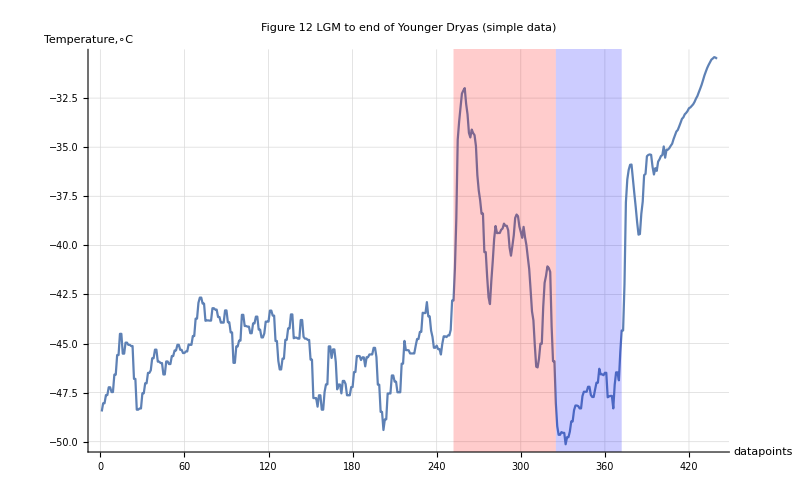

```mathematica
Show[
ListPlot[regulardataPart ,GridLines->Automatic,Joined->True,PlotRange->All,AxesLabel->{RawBoxes["datapoints"],RawBoxes["Temperature,∘C"]},PlotLabel->"Figure 12 LGM to end of Younger Dryas (simple data)",LabelStyle->{GrayLevel[0],Bold},ImageSize->800],
Plot[-60,{x,325,372},PlotStyle->Blue,Filling->Axis],
Plot[-60,{x,252,325},PlotStyle->Red,Filling->Axis]
]
```

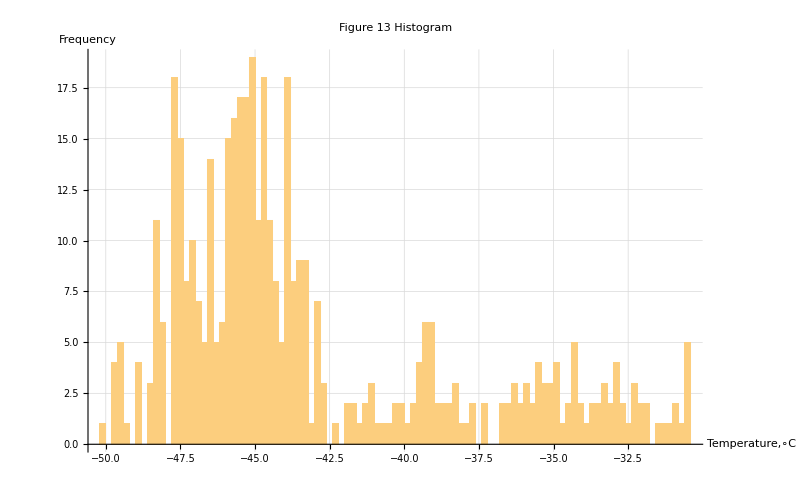

```mathematica
Histogram[regulardataPart,100,PlotRange->All,AxesLabel->{RawBoxes["Temperature,∘C"],RawBoxes["Frequency"]},GridLines->Automatic,PlotLabel->"Figure 13 Histogram",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

439

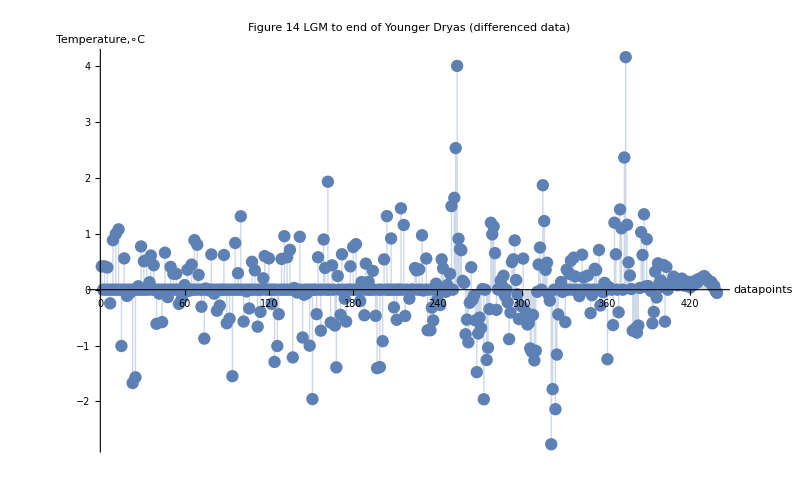

```mathematica
diffdataPart= Differences[regulardataPart];
Length[diffdataPart]
ListLinePlot[diffdataPart,Joined->False,Filling->Axis,PlotRange->All, AxesLabel->{RawBoxes["datapoints"],RawBoxes["Temperature,∘C"]},PlotLabel->"Figure 14 LGM to end of Younger Dryas (differenced data)",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

### 5.1 Variance

**Note that rolling window plot is modified such that it shows the events where abrupt changes occur, with red dashed line indicates the start of Bølling Allerød warming, and blue dashed line denotes the end of Younger Dryas. Last 25 data points are also been cropped so that the resultant graph focus more on the changes before transitions.

```mathematica
windowPlot2[data_,window_,f_,plegend_,color_,plabel_,xlabel_,ylabel_]:= Module[{movingmap,xAxis,windowedData,graph,plot},
movingmap = MovingMap[f, data[[1;;Length[data]-25]],window];
xAxis = Range[window,Length[data]];
windowedData =  Table[{xAxis[[i]],movingmap [[i]]},{i,Length[movingmap ]}];
graph=ListLinePlot[windowedData, GridLines->{{{372,Directive[Blue,Thick,Dashed]},{252,Directive[Red,Thick,Dashed]}},Automatic},PlotStyle->{color},PlotRange->{{0,Length[data]},Full},PlotLegends->{plegend}];
plot = Show[graph,AxesLabel->{RawBoxes[xlabel],RawBoxes[ylabel]},PlotLabel->plabel,LabelStyle->{GrayLevel[0],Bold},ImageSize->800];
plot]
```

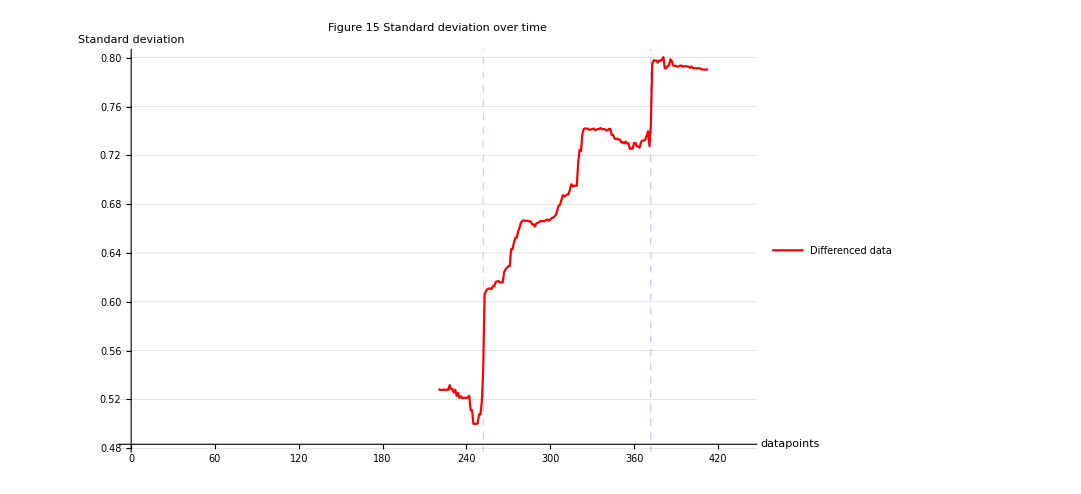

```mathematica
windowPlot2[diffdataPart,220,StandardDeviation,"Differenced data",Red,"Figure 15 Standard deviation over time","datapoints","Standard deviation"]
```

Discussion of the result in this part will be discussed together with next part (5.2).

### 5.2 Autocorrelation

```mathematica
ACF1[data_]:=CorrelationFunction[data,1];
```

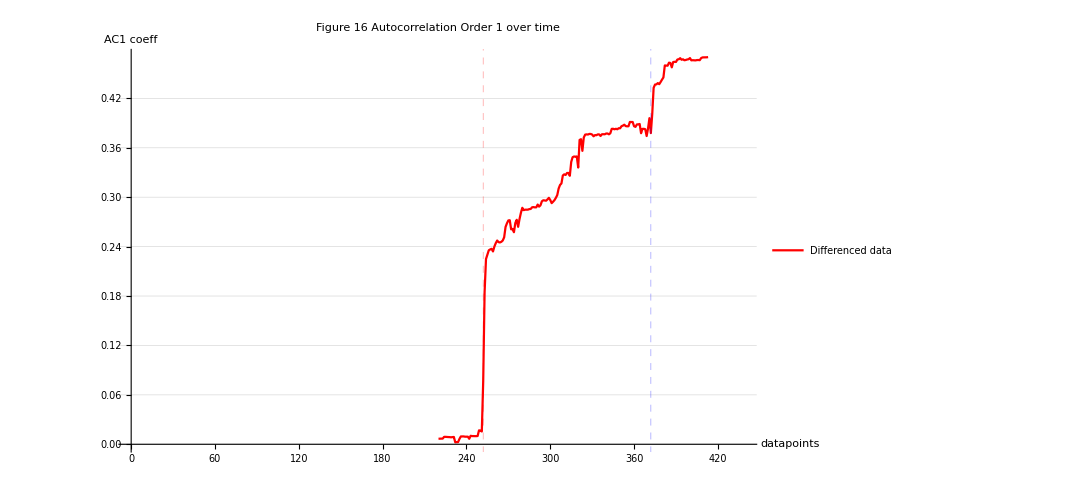

```mathematica
windowPlot2[diffdataPart,220,ACF1,"Differenced data",Red,"Figure 16 Autocorrelation Order 1 over time","datapoints","AC1 coeff"]
```

Both variance and autocorrelation graphs show a clear increase trend towards the end of of Younger Dryas (see Figure 15 and 16). As the window size is very large (half of the length of data), it is hard to tell, at least from these figures, if there are any signs of slowing down for Bølling Allerød warming.

### 5.3 Skewness

The skewness is a dimensionless measure of the degree of asymmetry of a probability distribution in which it vanishes for distribution symmetric about the mean and is positive or negative for an asymmetric distribution with a tail above or below the mean respectively. [o] The authors in [o] suggested that it is the change in skewness which acts as an early warning signal, and could be from zero skewness to either positive or negative values or from one sign of skewness to the other.

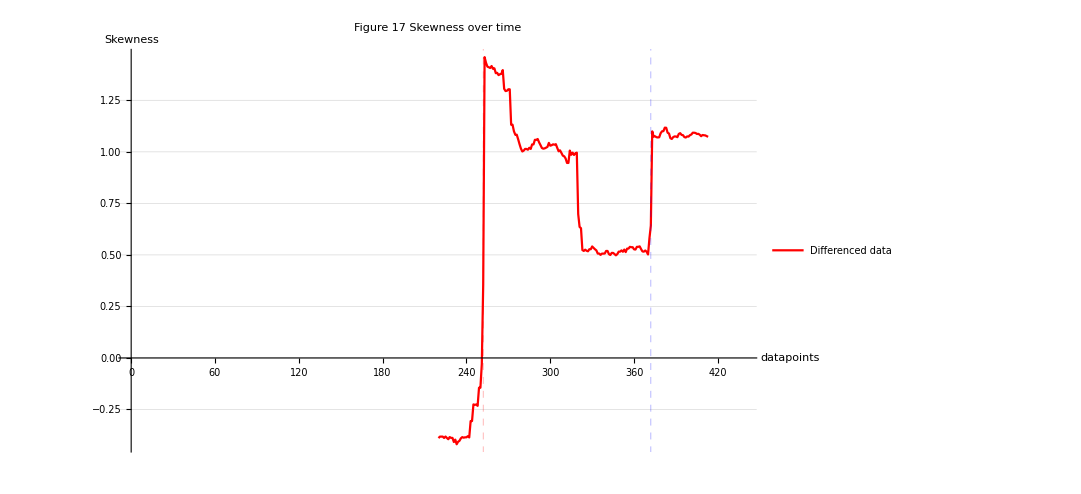

```mathematica
windowPlot2[diffdataPart,220,Skewness,"Differenced data",Red,"Figure 17 Skewness over time","datapoints","Skewness"]
```

There is an increase in and hence a change of skewness from negative to positive values for Bølling Allerød warming (see Figure 17). The skewness of the system shows a decrease in general before the end of Younger Dryas, however, the values are still positive. Hence, based on the interpretation from [o], using skewness as an indicator shows an early warning signal for Bølling Allerød warming but not end of Younger Dryas.

### 5.4 Kurtosis

As mentioned, approaching tipping  points, the variance of the system increases. Thus it enhances the tail of the distribution. Kurtosis is the measure of the tailedness of the distribution, so it is also used as an early warning signal for predicting tipping points. [p] It is expected to see a decrease in kurtosis near tipping points. It is observed that the kurtosis of system in fact shows a drop near the period of the end of Younger Dryas (see Figure 18).

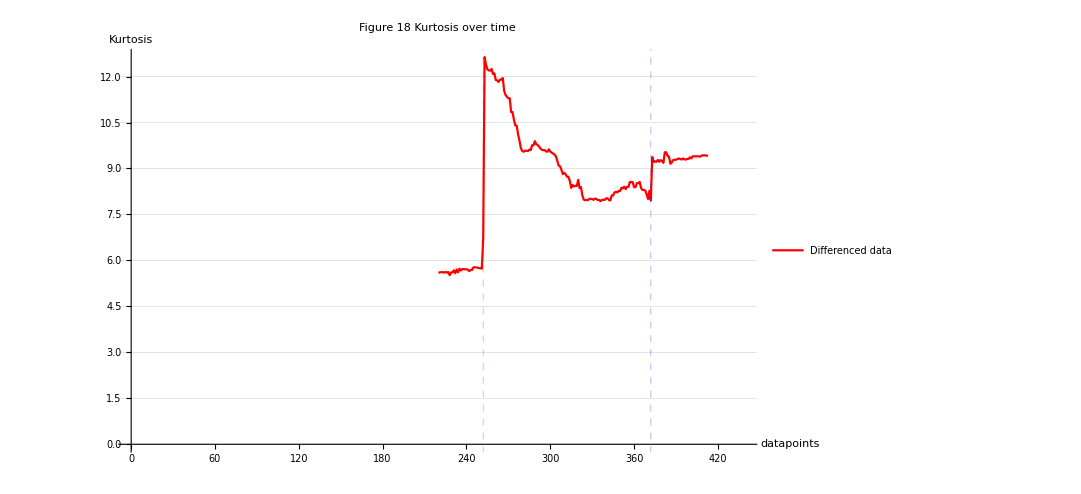

```mathematica
windowPlot2[diffdataPart,220,Kurtosis,"Differenced data",Red,"Figure 18 Kurtosis over time","datapoints","Kurtosis"]
```

## 6. Comparative Analysis of dataset

In this section, the real time series is detrended by using Gaussian kernel with a range of smoothing levels, r. The purpose is to apply the complexity measures in Section 4 such as SampEn and burstiness to the smoothed data, as a comparative analysis of complex time series with linear data. The comparative analyses of data are carried out by plotting measures of complexity value vs degree of smoothing. In the end of this section, a RP  is constructed for the data with highest level of r, again, as a comparison with the original time series. Note that in Section 2, stationary version of data is used in application of SampEn and burstiness, hence, differenced data of linear data is also employed for the mentioned measures.

### 6.1 Detrend time series using Gaussian Kernel Filter

This part is to show the higher the smoothing factor, the more linear data is produced.

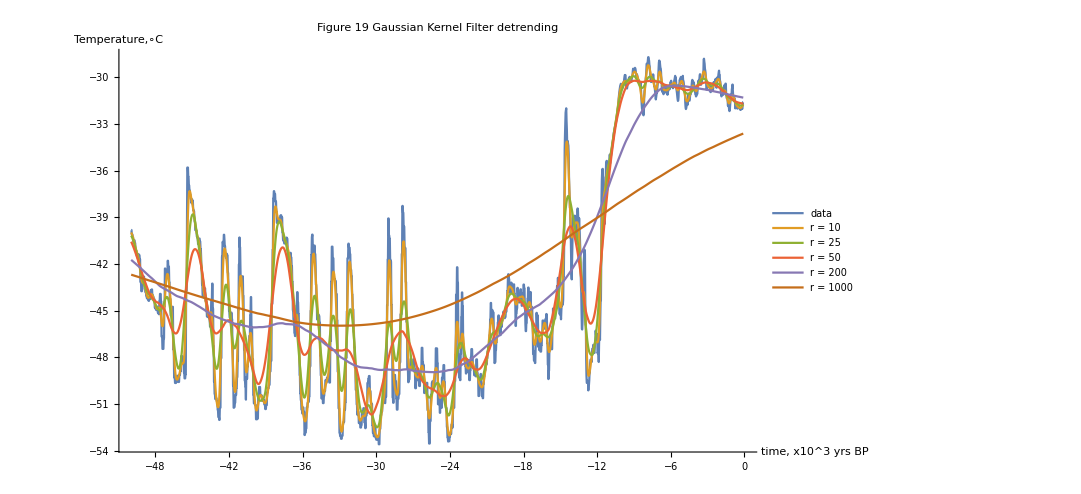

```mathematica
res=Table[GaussianFilter[tsReg,r],{r,{10,25,50,200,1000}}];
ListLinePlot[Join[{tsReg},res],ScalingFunctions->{"Reverse",Identity},PlotLegends->{"data","r = 10","r = 25","r = 50","r = 200","r = 1000"},AxesLabel->{RawBoxes["time, x10^3 yrs BP"],RawBoxes["Temperature,∘C"]},PlotLabel->"Figure 19 Gaussian Kernel Filter detrending",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

### 6.2 Measures of complexity of linear data

#### 6.2.1 Sample Entropy and burstiness

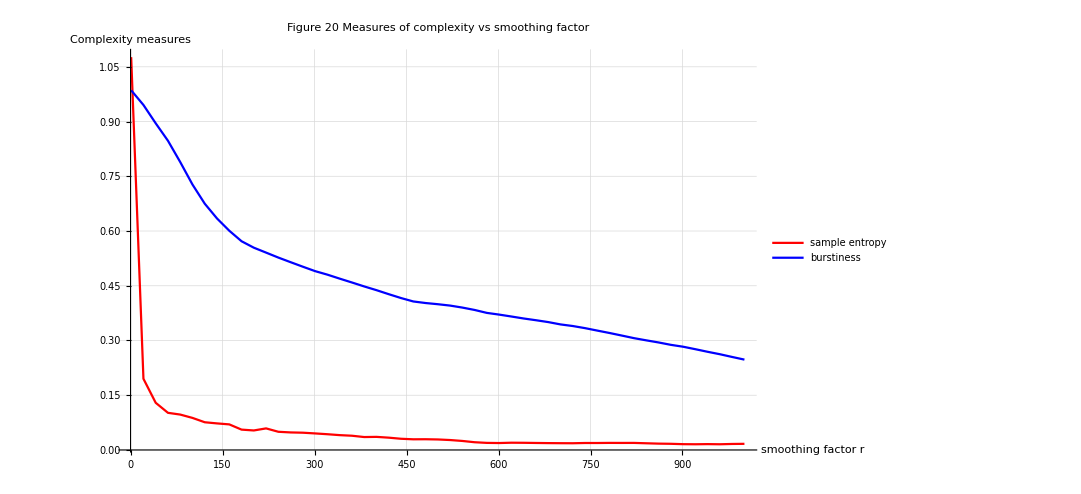

```mathematica
SampEncompare=Table[SampEn[Differences[GaussianFilter[tsReg,r]["Values"]]],{r,1,1001,20}];
rValues = Range[1,1001,20];
dataSampEn =Transpose@{rValues,SampEncompare};
s1 = ListLinePlot[dataSampEn , PlotRange->All,GridLines->Automatic,PlotStyle->{Red},PlotLegends->{"sample entropy"}];

burstcompare=Table[burstiness[Differences[GaussianFilter[tsReg,r]["Values"]]],{r,1,1001,20}];
databurst =Transpose@{rValues,burstcompare};
b1 =ListLinePlot[databurst,PlotRange->All, GridLines->Automatic,PlotStyle->{Blue},PlotLegends->{"burstiness"}];

Show[{s1,b1},PlotRange->All,AxesLabel->{RawBoxes["smoothing factor r"],RawBoxes["Complexity measures"]},PlotLabel->"Figure 20 Measures of complexity vs smoothing factor",LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

Figure 20 depicts that the higher linearity, the lower complexity of data in terms of sample entropy and burstiness. It also justifies that the original data (without any degree of detrending) is indeed complex and non-linear.

#### 6.2.2 Recurrence plot

```mathematica
(*Extract one timeseries from Section 6.1*)
lineardata = res[[5]]["Values"]; (*when r = 1000*)
0.15*StandardDeviation[lineardata]
```

0.573421

```mathematica
ϵ=0.01;  

g7=MatrixPlot[Table[1-UnitStep[ϵ-Norm[lineardata⟦t⟧-lineardata⟦τ⟧]],
{t,1,Length[lineardata]},{τ,1,Length[lineardata]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Full"];

g8=MatrixPlot[Table[1-UnitStep[ϵ-Norm[lineardata⟦t⟧-lineardata⟦τ⟧]],
{t,1,600},{τ,1,600}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Top Left (1-600 datapoints)"];

g9=MatrixPlot[Table[1-UnitStep[ϵ-Norm[lineardata⟦t⟧-lineardata⟦τ⟧]],
{t,600,1320},{τ,600,1320}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Centre (600-1320 datapoints)"];

g10=MatrixPlot[Table[1-UnitStep[ϵ-Norm[lineardata⟦t⟧-lineardata⟦τ⟧]],{t,1200,Length[lineardata]},
{τ,1200,Length[lineardata]}],Mesh->False,FrameLabel->TraditionalForm/@{t,τ}, PlotLabel->"Bottom Right (1200-1996 datapoints)"];

Show[GraphicsGrid[{{g7,g8},{g9,g10}}], PlotLabel-> Style["Figure 21 Recurrence Plot with distance = 0.01 (linear data)","Subsubsection"]]
```

-Graphics-

```mathematica
ϵ=0.01;
rp =Table[UnitStep[ϵ-Norm[lineardata⟦t⟧-lineardata⟦τ⟧]],{t,1,Length[lineardata]},{τ,1,Length[lineardata]}];
n=Length[lineardata];
countlines=0;
countpoints=0;
For[j=0,j<n,j++,
linelength=0;
For[i=1,i+j<n,i++,
If[rp[[i,i+j+1]]==1,linelength++,
If[linelength≥2,countlines++,
If[linelength==1,countpoints++
];
];
linelength=0(*reset for a diagonal*)
];
];
If[linelength≥2,countlines++,
If[linelength==1,countpoints++
];
];
];
pr=N[(Total[Total[rp]])/(n*n)];
pd=N[2*countlines/(n*n)];
dr=N[pd/pr];
Print[StringJoin["Recurrence Rate (RR): ",ToString[pr]]];
Print[StringJoin["Determinisim(DET): ",ToString[dr]]];
```

Recurrence Rate (RR): 0.0044794

Determinisim(DET): 0.088087

Figure 21 shows the recurrence plot of detrended time series with a factor of 1000, a big contrast with what is observed in Figure 4, where no patterns are seen. The RR and DET measured are 0.004 and 0.09 respectively, which are much lower than the values before (0.12 and 0.16).

## 7. Conclusion

In conclusion, in time series analysis, the dynamics and complexity of whole paleoclimate record from Greenland ice core are studied, and almost all of them show significant transition either in pattern (RP) or values (Hurst, SampEn, Burstiness) at the end of Younger Dryas. For detection of critical slowing down in period from Last Glacial Maximum to the end of Younger Dryas, strong signs of early warning are spotted for the end of Younger Dryas using indicator such as standard deviation, autocorrelation and kurtosis, while the abrupt change in warming of Bølling Allerød has only one positive result with indicator skewness. These results are somewhat parallel to previous studies, where [b,c] had found a positive trend in variability and autocorrelation for the end of Younger Dryas and a weak early sign in autocorrelation for the starting of Bølling Allerød. Then, the comparative analysis of the time series affirms its non-linearity nature. Finally, it is suggested to extend the complexity analysis by diving deeper into RQA. Comparison of Approximate Entropy and Sample Entropy on current data can also be carried out as in [a,j].

## References

[1] https://en.wikipedia.org/wiki/Deglaciation
[2] https://en.wikipedia.org/wiki/Dansgaard%E2%80%93Oeschger_event
[3] https://en.wikipedia.org/wiki/B%C3%B8lling%E2%80%93Aller%C3%B8d_warming
[4] https://en.wikipedia.org/wiki/Younger_Dryas
[5] https://en.wikipedia.org/wiki/Last_Glacial_Maximum
[6] Lenton, T. & Livina, Valerie & Dakos, Vasilis & Scheffer, M.. (2012). Climate bifurcation during the last deglaciation. Climate of the Past Discussions. 8. 321-348. 10.5194/cpd-8-321-2012. 
[7] Alley R (2004) GISP2 Ice Core Temperature and Accumulation Data. IGBP PAGES/World .Data Center for Paleoclimatology Data Contribution Series no. 2004-013.
NOAA/NGDC Paleoclimatology Program, Boulder CO.
[a] Delgado-Bonal, A., Marshak, A., Yang, Y. et al. Analyzing changes in the complexity of climate in the last four decades using MERRA-2 radiation data. Sci Rep 10, 922 (2020). https://doi.org/10.1038/s41598-020-57917-8
[b] Dakos, Vasilis & Scheffer, Marten & Nes, Egbert & Brovkin, Victor & Petoukhov, V. & Held, Hermann. (2008). Slowing down as an early warning signal for abrupt climate change. Proceedings of the National Academy of Sciences of the United States of America. 105. 14308-12. 10.1073/pnas.0802430105. 
[c] Lenton, T & Livina, Valerie & Dakos, Vasilis & Nes, E & Scheffer, M. (2012). Early warning of climate tipping points from critical slowing down: Comparing methods to improve robustness. Philosophical transactions. Series A, Mathematical, physical, and engineering sciences. 370. 1185-204. 10.1098/rsta.2011.0304. 
[d] Marwan, Norbert & Romano, Maria & Thiel, Marco & Kurths, Juergen. (2007). Recurrence Plots for the Analysis of Complex Systems. Physics Reports. 438. 237-329. 10.1016/j.physrep.2006.11.001. 
[e] Bastos, João & Caiado, Jorge. (2011). Recurrence quantification analysis of global stock. Physica A-statistical Mechanics and Its Applications - PHYSICA A. 390. 10.1016/j.physa.2010.12.008. 
[f] Zhang, Wen & Feng, Guoling & Liu, Qunqun. (2016). The Application of Recurrence Quantification Analysis in Detection of Abrupt Climate Change. Discrete Dynamics in Nature and Society. 2016. 1-7. 10.1155/2016/2689429. 
[g] Güldal, Serkan & Baugh, Veronica. (2015). Dynamic System Analysis Using Recurrence Quantification Analysis and Recurrence Plots In Mathematica.
[h] Rehman S, Study of Saudi Arabian climatic conditions using Hurst exponent and climatic predictability index, Chaos, Solitons & Fractals (2007), doi:10.1016/j.chaos.2007.01.079
[i] https://mathematica.stackexchange.com/questions/162634/can-this-sample-entropy-sampen-calculation-be-improved
[j] Delgado-Bonal A, Marshak A. Approximate Entropy and Sample Entropy: A Comprehensive Tutorial. Entropy. 2019; 21(6):541.
[k] Michael Harré (2019). Highly rational to wildly irrational: Housing markets are a heterogeneous ensemble.
[l] https://en.wikipedia.org/wiki/Burstiness
[m] https://en.wikipedia.org/wiki/Coefficient_of_variation
[n] Scheffer, Marten & Carpenter, Stephen & Lenton, Timothy & Bascompte, Jordi & Brock, William & Dakos, Vasilis & van de Koppel, Johan & van de Leemput, Ingrid & Levin, Simon & Nes, Egbert & Pascual, Mercedes & Vandermeer, John. (2012). Anticipating Critical Transitions. Science (New York, N.Y.). 338. 344-8. 10.1126/science.1225244. 
[o] Guttal, V. & Jayaprakash, Ciriyam. (2008). Changing skewness: an early warning signal of regime shift in ecosystems. Ecology Letters. 201. 420-428. 
[p ] Nazarimehr, Fahimeh & Jafari, Sajad & Golpayegani, Seyed & Perc, Matjaž & Sprott, Julien Clinton. (2018). Predicting tipping points of dynamical systems during a period-doubling route to chaos. Chaos: An Interdisciplinary Journal of Nonlinear Science. 28. 073102. 10.1063/1.5038801.